```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
T1[t_]:=T1[t]=t*IdentityMatrix[1]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.01,1,0]],A:=Inverse[β[ω,0.01,1,0]],B:=Inverse[β[ω,0.01,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[1]-A.T1.Inverse[IdentityMatrix[1]-B.T2.J.T2].B.T1].A,4000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]]
```

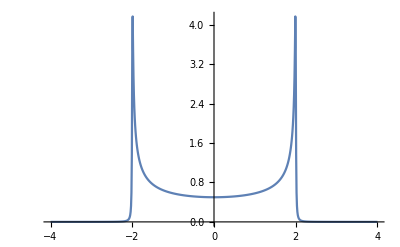

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0][[1,1]]]},{ω,Range[-4,4,0.01]}],PlotRange->All]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:= Inverse[(ω+ⅈ*δ-ϵ1)IdentityMatrix[1]]
```

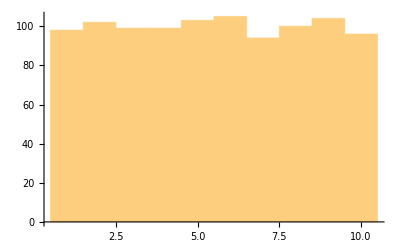

```mathematica
Histogram[Table[RandomChoice[Range[1,10,1]],1000]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,m_,n_,o_,p_]:=Module[{gg=g[ω,δ,t,ϵ],T=t*IdentityMatrix[1],imp=imp[ω,δ,t,ϵ,ϵ1]},sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,n]; J=J];sl2=Inverse[IdentityMatrix[1]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,m]; J=J];sl4=Inverse[IdentityMatrix[1]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,o]; J=J];sl6=Inverse[IdentityMatrix[1]-imp.T.sl5.T].imp; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,p]; J=J];Il1:=Inverse[IdentityMatrix[1]-sl7.T1[1].SR[ω,0.001,1,0].T1[1]].sl7;
Ir1:=Inverse[IdentityMatrix[1]-SR[ω,δ,1,0].T1[1].sl7.T1[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

```mathematica
RandomInteger[{0,25}]
```

7

```mathematica
f[ϵ1_]:=Table[{ω,Mean[Table[tr1[ω,0.01,1,0,ϵ1,RandomInteger[{0,25}],RandomInteger[{0,25}],RandomInteger[{0,25}],RandomInteger[{0,25}]],10000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
Export["1d3imp1.csv",f[1]]
```

1d3imp1.csv

```mathematica
Export["1d3imp3.csv",f[0.3]]
```

1d3imp3.csv

```mathematica
Export["1d3imp4.csv",f[0.4]]
```

1d3imp4.csv

```mathematica
Export["1d3imp5.csv",f[0.5]]
```

1d3imp5.csv

```mathematica
Export["1d3imp6.csv",f[0.6]]
```

1d3imp6.csv

```mathematica
Import["1d3imp6.csv"]
```

{{0.,0.865906},{0.01,0.869259},{0.02,0.873945},{0.03,0.874861},{0.04,0.874828},{0.05,0.873647},{0.06,0.872934},{0.07,0.870133},{0.08,0.867254},{0.09,0.867805},{0.1,0.868004},{0.11,0.866948},{0.12,0.867202},{0.13,0.868914},{0.14,0.870245},{0.15,0.870776},{0.16,0.870668},{0.17,0.869478},{0.18,0.869432},{0.19,0.868609},{0.2,0.86661},{0.21,0.864406},{0.22,0.864256},{0.23,0.863915},{0.24,0.863615},{0.25,0.863222},{0.26,0.862944},{0.27,0.863233},{0.28,0.863591},{0.29,0.863952},{0.3,0.864567},{0.31,0.863502},{0.32,0.864906},{0.33,0.866063},{0.34,0.866971},{0.35,0.866998},{0.36,0.867356},{0.37,0.869025},{0.38,0.866828},{0.39,0.866746},{0.4,0.867297},{0.41,0.866463},{0.42,0.866548},{0.43,0.863749},{0.44,0.86086},{0.45,0.86205},{0.46,0.861512},{0.47,0.859476},{0.48,0.860054},{0.49,0.859969},{0.5,0.859595},{0.51,0.859919},{0.52,0.862397},{0.53,0.86093},{0.54,0.863135},{0.55,0.862609},{0.56,0.861838},{0.57,0.863039},{0.58,0.86292},{0.59,0.862333},{0.6,0.862865},{0.61,0.86332},{0.62,0.864853},{0.63,0.861789},{0.64,0.863361},{0.65,0.860986},{0.66,0.860818},{0.67,0.859511},{0.68,0.85812},{0.69,0.85644},{0.7,0.85501},{0.71,0.8544},{0.72,0.856464},{0.73,0.855603},{0.74,0.856064},{0.75,0.85765},{0.76,0.856949},{0.77,0.856497},{0.78,0.855846},{0.79,0.8578},{0.8,0.858282},{0.81,0.860201},{0.82,0.857962},{0.83,0.857231},{0.84,0.859764},{0.85,0.859395},{0.86,0.856667},{0.87,0.854772},{0.88,0.854423},{0.89,0.852527},{0.9,0.852482},{0.91,0.851089},{0.92,0.852754},{0.93,0.849027},{0.94,0.850527},{0.95,0.849724},{0.96,0.852866},{0.97,0.851669},{0.98,0.850927},{0.99,0.851789},{1.,0.850696},{1.01,0.851895},{1.02,0.852874},{1.03,0.850337},{1.04,0.850004},{1.05,0.851835},{1.06,0.850813},{1.07,0.849767},{1.08,0.850143},{1.09,0.846513},{1.1,0.843165},{1.11,0.842986},{1.12,0.841099},{1.13,0.841085},{1.14,0.839388},{1.15,0.839598},{1.16,0.839801},{1.17,0.841394},{1.18,0.838656},{1.19,0.841249},{1.2,0.839536},{1.21,0.842424},{1.22,0.841247},{1.23,0.841545},{1.24,0.843391},{1.25,0.840835},{1.26,0.840781},{1.27,0.839952},{1.28,0.834904},{1.29,0.836137},{1.3,0.831561},{1.31,0.830711},{1.32,0.830469},{1.33,0.828589},{1.34,0.828421},{1.35,0.828315},{1.36,0.828936},{1.37,0.828241},{1.38,0.83081},{1.39,0.830455},{1.4,0.830295},{1.41,0.826754},{1.42,0.829177},{1.43,0.82959},{1.44,0.825386},{1.45,0.824785},{1.46,0.821703},{1.47,0.817014},{1.48,0.813055},{1.49,0.812226},{1.5,0.812485},{1.51,0.809531},{1.52,0.808329},{1.53,0.813527},{1.54,0.810782},{1.55,0.810944},{1.56,0.811224},{1.57,0.810798},{1.58,0.809716},{1.59,0.807222},{1.6,0.805143},{1.61,0.803161},{1.62,0.795856},{1.63,0.795214},{1.64,0.789363},{1.65,0.788979},{1.66,0.785098},{1.67,0.786631},{1.68,0.785651},{1.69,0.785547},{1.7,0.787376},{1.71,0.781648},{1.72,0.780072},{1.73,0.777459},{1.74,0.772425},{1.75,0.765153},{1.76,0.75457},{1.77,0.754069},{1.78,0.749183},{1.79,0.743649},{1.8,0.740279},{1.81,0.737985},{1.82,0.735919},{1.83,0.735463},{1.84,0.724617},{1.85,0.706395},{1.86,0.694135},{1.87,0.678767},{1.88,0.663598},{1.89,0.643314},{1.9,0.635198},{1.91,0.622143},{1.92,0.599947},{1.93,0.575306},{1.94,0.535494},{1.95,0.496387},{1.96,0.504793},{1.97,0.613641},{1.98,0.827257},{1.99,1.42746},{2.,0.267603},{2.01,0.350594},{2.02,0.137348},{2.03,0.151421},{2.04,0.074165},{2.05,0.184543},{2.06,0.22376},{2.07,0.408496},{2.08,1.02219},{2.09,8.07776},{2.1,0.451063},{2.11,0.258791},{2.12,0.130129},{2.13,0.0925568},{2.14,0.0250603},{2.15,0.103157},{2.16,0.0149396},{2.17,0.0206275},{2.18,0.0898143},{2.19,0.0118311},{2.2,0.00605338},{2.21,0.00913087},{2.22,0.0775693},{2.23,0.117726},{2.24,0.0163502},{2.25,0.0110623},{2.26,0.00178254},{2.27,0.00747794},{2.28,0.00152675},{2.29,0.00101428},{2.3,0.00049114},{2.31,0.000516453},{2.32,0.000321767},{2.33,0.00752878},{2.34,0.00026638},{2.35,0.000233436},{2.36,0.000205718},{2.37,0.000202042},{2.38,0.000174338},{2.39,0.000160466},{2.4,0.000150545},{2.41,0.000139376},{2.42,0.000131293},{2.43,0.000124756},{2.44,0.000116812},{2.45,0.000108915},{2.46,0.000102898},{2.47,0.000096361},{2.48,0.000091797},{2.49,0.0000870406},{2.5,0.0000828148},{2.51,0.0000788119},{2.52,0.0000751104},{2.53,0.0000708969},{2.54,0.0000681833},{2.55,0.0000650626},{2.56,0.0000616587},{2.57,0.0000596987},{2.58,0.0000566955},{2.59,0.0000548308},{2.6,0.0000523236},{2.61,0.0000503372},{2.62,0.0000485656},{2.63,0.0000465077},{2.64,0.000044691},{2.65,0.0000432607},{2.66,0.0000417709},{2.67,0.0000400998},{2.68,0.0000386988},{2.69,0.0000371719},{2.7,0.0000361641},{2.71,0.0000350283},{2.72,0.0000337407},{2.73,0.0000326648},{2.74,0.0000316129},{2.75,0.0000305061},{2.76,0.000029678},{2.77,0.0000287252},{2.78,0.0000278747},{2.79,0.0000268519},{2.8,0.0000261569},{2.81,0.0000253769},{2.82,0.0000245579},{2.83,0.0000238958},{2.84,0.000023195},{2.85,0.000022704},{2.86,0.0000219387},{2.87,0.0000213467},{2.88,0.0000208419},{2.89,0.0000201958},{2.9,0.0000196535},{2.91,0.0000191369},{2.92,0.0000185783},{2.93,0.0000182486},{2.94,0.0000177622},{2.95,0.0000173142},{2.96,0.0000168944},{2.97,0.0000164507},{2.98,0.0000160462},{2.99,0.0000156267},{3.,0.0000152794}}

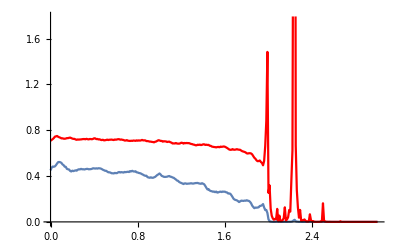

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/PhD/fwi/1D/1d5imp1.csv"]],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/1D/1d3imp1.csv"],PlotStyle->Red],PlotRange->All]
```

```mathematica
Export["1d3imp7.csv",f[0.7]]
```

1d3imp7.csv

```mathematica
Export["1d3imp8.csv",f[0.8]]
```

1d3imp8.csv

```mathematica
Export["1d3imp9.csv",f[9]]
```

1d3imp9.csv

```mathematica
L:={}
```

```mathematica
υ[ϵ1_,τ_]:=Module[{(*μ1=RandomInteger[{1,7}],μ2=RandomInteger[{1,7}],μ3=RandomInteger[{1,7}],μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}],μ6=RandomInteger[{1,7}],μ7=RandomInteger[{1,7}],μ8=RandomInteger[{1,7}]*)p=RandomInteger[{1,20}],q=RandomInteger[{1,20}],r=RandomInteger[{1,20}],s=RandomInteger[{1,20}],w=RandomInteger[{1,20}]},
(*Print[{μ1,μ2,μ3,μ4,μ5,μ6,μ7,μ8}];*)
η5:=Module[{gg=g[ω,0.01,1,0],T=1*IdentityMatrix[1],imp=imp[ω,0.01,1,0,ϵ1]},sl1= Module[{J=SL[ω,0.01,1,0]},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,p]; J=J];sl2=Inverse[IdentityMatrix[1]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,q]; J=J];sl4=Inverse[IdentityMatrix[1]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,r]; J=J];sl6=Inverse[IdentityMatrix[1]-imp.T.sl5.T].imp; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,s]; J=J];sl8=Inverse[IdentityMatrix[1]-imp.T.sl7.T].imp; sl9=Module[{J=sl8},Do[J=Inverse[IdentityMatrix[1]-gg.T.J.T].gg,w]; J=J];Il1:=Inverse[IdentityMatrix[1]-sl9.T1[1].SR[ω,0.01,1,0].T1[1]].sl9;
Ir1:=Inverse[IdentityMatrix[1]-SR[ω,0.01,1,0].T1[1].sl9.T1[1]].SR[ω,0.01,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,0.01,1,0].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];
Clear[m5];m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/1D/1d2imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/1D/1d3imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/1D/1d4imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/1D/1d5imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/1D/1d6imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/1D/1d7imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
(*ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/1D/1d5imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/1D/1d5imp4.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)];
*)(*ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/1D/10imp/10imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,τ}]/(τ*100)]*);
list:={{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7}(*,{8,ρ8},{9,ρ9}*)(*,{10,ρ10}*)};(*Print[list];*){list[[Position[list,Min[list]][[1,1]],1]],Min[list],p+q+r+s+3}]
```

```mathematica
Timing[υ[0.5,1.]]
```

{0.416696,{4,0.0000524254,28}}

```mathematica
f[τ_]:=f[τ]=Table[υ[0.5,τ],50]
```

```mathematica
Max[f[1.8]]
```

5

```mathematica
f[1.8]
```

{{4,0.00039778,15},{4,0.000158059,42},{3,0.0000931308,59},{4,0.000102204,35},{4,0.000115861,51},{3,0.0000625389,49},{3,0.0000576397,52},{4,0.000241532,34},{4,0.000112575,41},{4,0.0000841091,57},{3,0.0000677204,60},{3,0.000100821,37},{4,0.00011275,48},{4,0.000169139,36},{4,0.0000939473,36},{3,0.0000830835,49},{3,0.0000581519,57},{3,0.0000709958,48},{4,0.000203559,36},{4,0.0000980364,42},{4,0.000204389,46},{3,0.0000518308,56},{4,0.000173796,48},{4,0.000129004,53},{4,0.000251231,30},{4,0.000162675,46},{4,0.000174741,54},{4,0.000231001,32},{4,0.000115696,69},{4,0.000183502,38},{4,0.000115606,54},{4,0.0000970964,28},{3,0.0000736702,48},{4,0.000151382,37},{4,0.000207289,32},{3,0.000132697,44},{4,0.0000957009,32},{4,0.0000630737,42},{4,0.000134909,35},{4,0.00016593,51},{4,0.000176525,33},{4,0.00011441,41},{3,0.0000641681,44},{4,0.000136891,60},{4,0.000128583,47},{4,0.000123101,47},{4,0.0000968217,44},{3,0.0000678328,44},{4,0.0000992653,50},{4,0.0000926237,42}}

```mathematica
ϕ[τ_]:=2*(Count[Part[f[τ],;;,1],4]+Count[Part[f[τ],;;,1],5]+Count[Part[f[τ],;;,1],3])/100
```

```mathematica
Table[{τ,ϕ[τ]},{τ,0.1,2.5,0.1}]
```

{{0.1,14/25},{0.2,13/25},{0.3,17/25},{0.4,29/50},{0.5,19/25},{0.6,41/50},{0.7,47/50},{0.8,23/25},{0.9,47/50},{1.,1},{1.1,49/50},{1.2,49/50},{1.3,24/25},{1.4,1},{1.5,24/25},{1.6,49/50},{1.7,49/50},{1.8,1},{1.9,1},{2.,31/50},{2.1,1},{2.2,1},{2.3,1},{2.4,1},{2.5,1}}

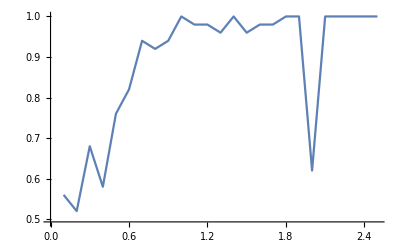

```mathematica
ListPlot[%31,Joined->True]
```

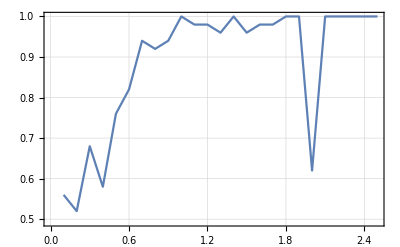

```mathematica
ListPlot[%31,PlotTheme->"Detailed",Joined->True]
```

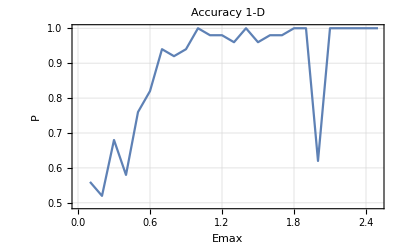

```mathematica
Show[%33,FrameLabel->{{HoldForm[P],None},{HoldForm[Emax],None}},PlotLabel->HoldForm[Accuracy 1-D],LabelStyle->{GrayLevel[0]}]
```

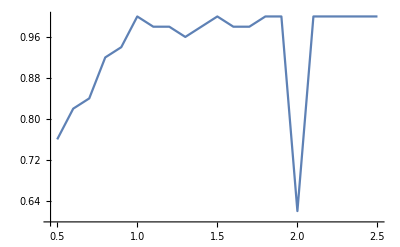

```mathematica
ListPlot[%29,Joined->True]
```

```mathematica
RandomReal[NormalDistribution[1,1/2],1000]
```

{1.03755,0.58127,1.32206,1.50175,0.927601,0.63021,0.807127,1.02043,0.98138,1.27872,2.22911,1.20065,0.370138,1.74643,1.77495,0.484411,1.08402,0.215188,0.884027,1.00147,0.709341,-0.075035,1.3809,0.961893,0.928669,0.892536,2.23057,1.79643,1.51439,1.25848,0.91637,1.27016,1.13103,0.231914,0.198036,1.08987,0.122256,0.291398,0.810306,1.05969,1.59151,0.725702,1.1111,1.45666,1.15516,1.67343,0.619136,-0.172366,1.31583,0.134084,0.889996,0.346274,0.777187,0.780557,0.836325,0.416067,1.06296,-0.0619226,0.159334,1.23712,1.56919,1.70415,0.109459,1.1792,1.30432,1.36367,1.55684,-0.114869,1.14514,0.2555,1.22411,0.64289,0.709485,0.49969,0.730002,1.14115,0.445055,1.39853,1.32321,0.762266,1.28501,1.55,1.41039,1.15434,0.575427,0.690142,1.78623,1.03524,0.479403,1.27223,-0.100716,0.406418,0.148571,0.813228,-0.0110427,1.01815,1.00252,0.699695,0.887856,1.27404,1.05522,1.89265,1.96172,0.576548,0.705005,1.27307,1.63097,1.31734,1.3459,0.829356,1.47003,1.3155,0.939685,1.80401,1.1409,1.59794,0.080689,0.144178,1.74846,0.102461,1.24056,0.338039,1.69855,0.418951,0.475678,0.758514,1.87136,0.556049,0.890315,0.424103,0.549468,1.30128,0.200918,2.11865,1.05638,0.953608,0.614406,0.41254,1.06892,0.6015,0.667091,1.441,1.46353,1.25511,1.61583,1.46436,0.418007,1.48887,0.500409,0.165218,1.24539,1.21731,0.444617,1.35447,1.17977,0.614132,1.24099,0.778182,1.33198,0.932187,0.524832,1.20615,1.80074,1.17741,0.409205,0.531666,0.655765,0.995589,1.01159,-0.364906,1.90754,0.340415,0.686176,0.94208,0.572625,1.60167,1.08648,0.863672,1.41376,0.591313,0.410786,0.597478,1.09929,1.54605,1.5589,0.519251,0.696423,1.05432,1.25009,0.314573,0.0513946,1.66736,1.03868,0.341433,0.477136,1.03577,1.43735,1.46965,0.863811,0.453719,0.365955,0.0600333,1.28573,1.39098,0.982723,0.797235,0.9394,1.06029,1.01264,2.70167,0.311642,0.998785,1.14912,1.23212,0.915177,0.272583,0.972537,1.3018,0.0410681,1.49051,0.521362,0.519195,0.610431,0.0471874,0.974351,1.81556,0.715306,1.27441,1.21551,1.17465,1.10944,0.845014,1.00429,0.87131,0.642037,1.09285,1.07299,0.883181,0.876649,1.00865,0.956188,1.58334,0.859149,2.29577,0.967332,0.954347,1.62564,1.28597,1.14442,1.07787,1.34838,0.933293,1.31783,1.38415,1.65982,1.36166,0.647644,1.18184,1.44827,1.59643,0.834841,1.07537,0.958971,0.93154,1.36284,1.73378,1.94833,0.121707,1.33972,0.781057,0.975099,0.85055,0.710943,0.348478,1.81148,0.410689,0.845961,1.57099,0.83003,1.1159,0.812879,1.23315,0.47755,0.762954,1.81954,1.4496,1.28153,1.92765,1.82028,1.0878,1.66461,0.620421,0.968274,2.26172,0.267331,1.30996,1.10878,0.977209,2.15478,0.219023,1.01927,0.836269,1.66952,0.422631,0.936465,1.56985,0.7893,0.618255,0.366032,0.590831,0.985785,-0.357037,0.579753,1.43567,1.98452,0.894469,1.11979,2.10033,1.23311,1.49987,0.56876,1.61573,1.44288,0.561526,0.387888,1.88495,0.298164,0.710985,1.09908,1.32649,0.825757,2.26589,1.41314,1.15281,0.314374,1.26711,0.862706,1.14718,0.0792288,0.850982,1.17864,1.62322,0.953036,-0.139586,0.358958,0.980152,0.440189,0.789295,1.5177,1.32718,1.03692,1.36817,0.985352,1.12957,1.02926,0.52039,1.1809,1.25347,0.0989489,0.0605247,0.582,1.19785,0.49581,1.04664,1.48398,0.929591,1.56274,1.28775,1.2566,1.04301,0.785661,0.200656,1.03821,0.967291,0.210753,1.13354,1.20269,-0.458879,0.579157,-0.320263,0.977127,0.4278,0.422014,1.15467,0.905017,0.81694,1.41363,1.43694,0.682008,1.3778,1.78041,0.51492,2.01829,0.673696,1.00459,0.997894,0.514455,0.742494,0.550557,1.13952,0.486353,0.818758,0.964058,1.18635,0.609228,1.25027,0.558699,1.38757,1.51051,1.30486,1.18701,1.16776,1.30664,0.944767,1.75778,1.58307,1.52927,1.29751,0.41259,0.497773,1.25002,0.468601,0.303164,1.52224,0.460733,0.789195,0.734422,0.139118,0.669038,1.1135,0.316338,1.07132,1.37195,1.8813,0.965505,0.685694,1.18572,1.44061,0.48136,1.08239,1.26569,0.754585,0.505885,1.77668,0.881531,1.64402,0.944354,1.0988,0.570464,1.81067,1.09052,1.06858,0.931503,1.67785,0.431399,1.492,1.54421,0.225119,0.91277,1.27903,1.32166,0.948708,0.961122,2.46994,0.430306,1.81836,1.08997,1.0389,1.29813,1.22733,1.08741,1.12482,0.766684,1.26729,1.00015,0.538641,1.05043,2.21327,1.19597,0.722938,0.794549,1.00273,2.42047,-0.19421,0.0154451,1.19842,1.26045,0.347271,1.10421,1.16969,1.48622,0.603367,0.421889,0.813545,0.911899,0.732536,0.594259,1.33816,1.56057,0.381552,-0.420678,0.390094,1.47719,0.755269,0.128641,0.545864,1.27049,-0.0338922,0.350217,0.876803,1.3369,1.23126,0.684591,0.288519,1.17243,2.37429,1.73366,2.11534,0.595539,0.787949,1.70732,0.887445,1.2645,1.66639,0.498368,1.12637,-0.255408,1.59236,0.802852,1.5174,0.462788,0.666448,0.408855,0.951929,0.237086,0.812922,2.02475,0.750944,0.323632,1.11174,0.87306,1.55213,0.659209,0.627019,1.33963,1.38532,0.785106,1.10022,1.30769,1.32921,0.826502,0.769723,1.29582,0.797535,0.853096,0.413061,0.310046,1.19116,0.732123,0.635754,-0.205175,0.322282,2.19899,1.06668,0.240498,0.937947,0.932004,0.0510479,1.92215,0.956226,0.279315,0.750717,1.87056,0.621695,1.53074,0.482573,1.02667,0.413147,0.887909,0.875513,0.876334,0.301951,1.20693,1.70743,1.64343,0.0375802,1.14013,0.889686,1.22137,1.52904,1.09046,0.879079,0.427382,1.15224,0.883401,0.516875,0.929868,1.59852,0.810999,0.41465,1.23191,1.39205,1.24166,1.51932,0.693093,0.767525,0.728052,0.811729,0.905929,1.25232,0.738738,0.775362,0.994029,1.48895,1.63312,1.58592,1.92984,0.297252,1.17839,1.59369,0.908948,-0.0651515,1.13098,0.792816,1.14655,0.790268,1.04654,0.234738,1.08805,0.731181,1.14573,0.824612,0.36923,0.87785,0.579575,1.38975,0.936345,0.536529,0.444139,0.130688,0.382139,1.40351,1.44551,1.65781,0.584877,1.01843,0.656947,0.721408,0.521469,0.556201,0.725507,0.873196,0.965737,0.479432,0.333209,0.766439,0.946982,1.30669,1.74758,0.41256,0.785312,0.717884,0.669609,1.09933,1.32577,0.747635,1.52367,1.72267,0.0695958,1.35616,0.866981,1.17395,0.782376,0.955871,0.704122,0.92744,1.55908,1.0364,1.33789,1.38995,0.7532,1.54842,0.792561,1.21932,1.55219,0.710109,1.23919,0.626879,0.784589,1.39588,2.0244,1.54908,1.15758,0.840537,0.166754,1.53635,1.08321,1.15793,0.499494,1.29679,1.48415,1.17191,0.338081,1.13298,1.17647,0.499358,1.41384,1.6519,1.22841,-0.080861,0.580202,1.57491,0.939206,0.517441,1.20617,0.233832,1.03769,1.55582,1.66084,1.62288,0.393293,0.135695,0.862598,1.23459,1.39642,0.919661,0.763971,1.26064,0.613432,0.983458,0.697295,0.706353,0.765655,0.887137,0.7681,1.2741,0.356315,0.920769,0.109848,1.39517,1.18578,0.508536,1.4301,1.01158,1.00823,0.582082,1.40725,0.202406,1.03159,0.77184,1.33928,1.48285,1.4328,1.08841,1.27885,0.361104,-0.164521,0.981592,1.05065,1.57756,1.20171,-0.28445,1.30933,1.27714,1.38986,1.47071,0.587142,0.6252,0.180116,-0.10389,0.490511,0.53321,0.109436,0.604917,1.37346,1.54096,1.48985,0.86226,0.819688,0.786922,2.0658,0.852738,1.11639,0.407121,0.59456,0.978509,0.672473,0.914737,0.511479,1.32542,0.65868,0.925796,1.3695,0.974899,1.00999,1.46631,0.126148,0.238305,0.521626,1.45792,1.46818,0.868524,0.879416,0.988203,0.839643,1.13812,1.81069,0.91442,0.22878,0.46363,1.29725,0.719859,0.168203,1.44597,1.09431,1.03714,0.787649,0.682954,1.60882,0.228151,1.04413,0.654802,0.972217,0.953272,2.05503,0.995713,1.22128,0.736287,0.74409,1.26446,0.199887,0.967095,0.536773,1.87891,1.89072,1.23992,1.17004,0.538195,0.620397,1.29282,0.594852,1.16064,0.45653,-0.0560027,2.27379,1.17271,0.660661,1.21238,1.75688,0.675455,0.770091,0.386588,-0.0637794,1.8215,1.01855,1.08102,0.242402,0.0468431,0.530161,1.33567,1.28893,0.794936,0.909713,0.604184,0.882727,0.240416,1.51759,1.36391,0.714079,0.807273,0.625404,1.45747,0.954613,1.25545,0.908188,0.705393,1.31238,0.118067,1.36079,1.13997,0.560493,1.13481,1.62388,1.79668,1.78141,2.3023,0.176301,1.25457,1.04627,1.09329,1.61892,0.557551,1.22602,0.514327,0.970853,0.703948,0.991173,0.242765,0.633787,1.58917,0.775837,1.11957,1.06321,1.22257,0.812733,1.37624,0.860501,1.32413,1.07283,0.683501,1.30992,0.979136,1.68678,1.266,0.398083,0.676786,0.89444,-0.487644,1.8606,0.665522,0.912803,0.654012,0.645425,0.980292,1.77392,0.471476,1.01887,1.50859,1.58316,0.820042,1.02411,0.399151,1.60017,1.50694,0.908444,-0.151265,-0.192145,0.699197,0.96166,1.47973,0.473073,0.995592,1.11084,1.54528,1.01892,1.37173,1.11162,1.10377,1.7046,0.728521,0.643317,0.926788,0.0399503,1.132,1.2095,1.58885,1.23653,1.63644,0.574574,1.74885,1.15117,1.60501,1.00046,1.33642,1.16356,1.3834,0.167022,0.671762,0.783086,0.93712,1.07374,0.999004,0.633834,0.792002,1.02496,1.04506,1.73344,1.47534,0.48341,0.181138,0.629657,0.816471,0.665761,0.345243,1.03355,1.34527,0.233483,1.14948,0.216865,0.212552,0.418406,1.27177,0.695746,1.68978,1.20364,0.735211,1.23755,0.65431,0.922701,0.50458}

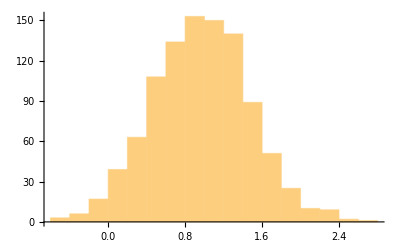

```mathematica
Histogram[%34]
```

```mathematica
UniformDistribution[Range[1,20,1]]
```

UniformDistribution[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}]

```mathematica
RandomReal[UniformDistribution[Range[1,20,1]],100]
```

RandomReal::parb: {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20} should have between 0 and 2 parameters.

RandomReal[UniformDistribution[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}],100]

Fit::fitd: First argument QuantityMagnitude[{{0.,0.},{0.0024288,0.},{0.00485759,0.},{0.00971519,0.},{0.0202476,0.},{0.030082,0.},{0.0397235,0.},{0.0501822,0.},{0.0599429,0.},{0.0705208,0.},{0.0809058,0.},{0.0905928,0.},{0.101097,0.},{0.110903,0.},{0.120517,0.},«21»,{0.343305,0.},{0.353027,0.},{0.363566,0.},{0.373407,0.},{0.383055,0.},{0.39352,0.},{0.403287,0.},{0.413872,0.},{0.424264,0.},{0.433957,0.},{0.444468,0.},{0.454281,0.},{0.463901,0.},{0.474338,0.},«71»}] in Fit is not a list or a rectangular array.

General::stop: Further output of Fit::fitd will be suppressed during this calculation.

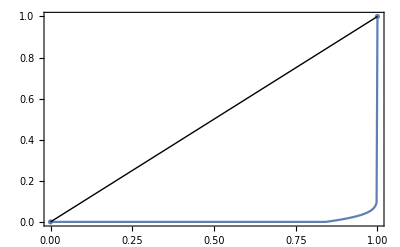

```mathematica
ProbabilityPlot[UniformDistribution[{1,20}]]
```

```mathematica
CDF[UniformDistribution[{1,20}],x]
```

Piecewise[{{1/19 (-1+x), 1≤x≤20}, {1, x>20}, {0, True}}]

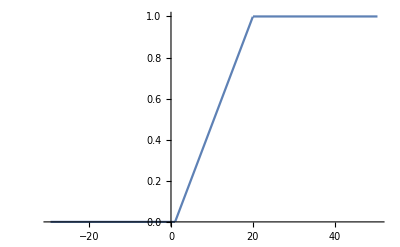

```mathematica
Plot[Piecewise[{{1/19 (-1+x),1≤x≤20},{1,x>20}},0],{x,-29.400000000000002,50.400000000000006}]
```

```mathematica
Histogram[Table[UniformDistribution[{1,20}],10000]]
```

-Graphics-

```mathematica
NormalDistribution[20,5]
```

NormalDistribution[20,5]

```mathematica
RandomVariate[NormalDistribution[20,5],100]
```

{33.3314,20.4761,16.859,25.4016,20.4424,11.7378,13.2661,16.1421,16.4135,25.1955,17.3702,22.1947,18.5667,21.2368,29.5276,31.2239,22.0352,18.9818,20.1688,27.9391,17.6551,22.0592,18.127,19.0473,23.494,24.2912,27.5098,18.2612,19.3517,21.3915,21.888,20.8502,28.6224,22.9695,24.8996,17.4137,22.8051,18.4343,19.6532,29.8878,21.5618,16.5935,26.7734,25.9265,19.4182,20.392,25.7177,23.9033,23.338,15.2673,23.3035,20.3805,23.9427,23.0522,20.9949,17.0307,33.3314,15.2404,18.2512,25.4802,14.9097,17.2106,12.4977,26.3052,23.1232,18.6812,26.5694,28.3175,16.412,16.0692,22.1959,19.6107,25.8437,15.0571,23.9274,11.3646,25.187,14.3808,20.9805,20.3327,26.5567,23.4462,16.0425,14.6869,18.3696,10.7118,19.331,19.0343,16.3449,23.2115,17.1504,16.0484,30.3963,14.3941,18.311,18.3504,17.3795,22.5429,19.7044,14.5695}

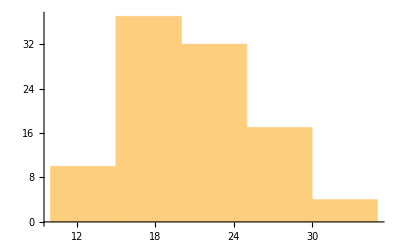

```mathematica
Histogram[%51]
```

```mathematica
Mean[NormalDistribution[20,5]]
```

20

```mathematica
Range[1,20,1]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

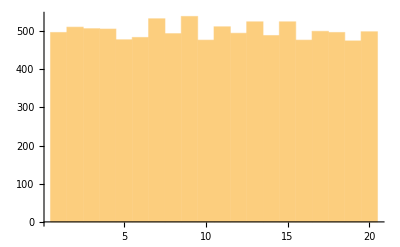

```mathematica
[Table[RandomChoice[Range[1,20,1]],10000]]
```

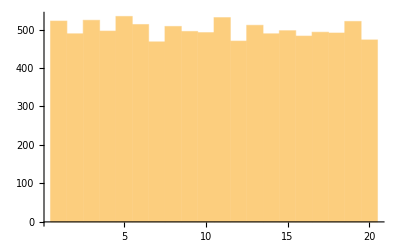

```mathematica
Histogram[Table[RandomInteger[{1,20}],10000]]
```

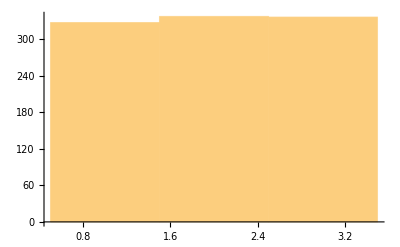

```mathematica
Histogram[%61]
```

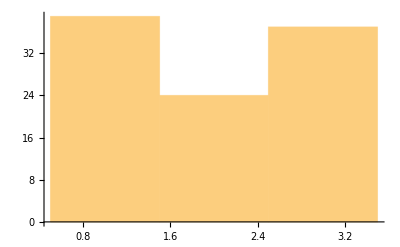

```mathematica
Histogram[%59]
```

```mathematica
RandomSample[%57]
```

{b,a,b,a,b,c,b,a,b,a,b,c,b,c,c,b,a,c,c,b,c,c,a,a,b,c,c,c,b,b,b,c,b,c,b,a,a,b,b,a,c,a,a,b,c,a,b,b,a,c,b,c,b,b,a,c,a,a,b,b,c,a,a,b,a,a,c,c,a,b,c,a,b,c,b,b,a,b,b,b,c,b,a,c,c,b,c,b,a,a,a,a,c,c,a,a,b,b,a,a}

```mathematica
f[a_,b_,i_]:=Table[{RandomInteger[{a,b}],RandomInteger[{a,b}],RandomInteger[{a,b}],RandomInteger[{a,b}]},10*b][[RandomInteger[{1,b*10}],i]]
```

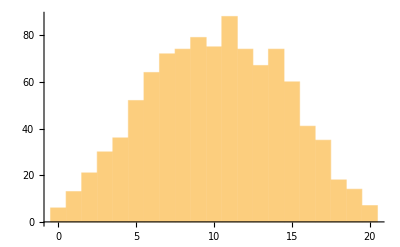

```mathematica
Histogram[Table[f[1]+f[2],1000]]
```

```mathematica
Dimensions[%81]
```

{100,4}